## Biped Description

-Graphics-

Based on the compass-gait model above [1].

[1] Rosa, N, B. Katamish, M. Raff, M., and C. D. Remy, “An Approach for Generating Families of Energetically Optimal Gaits from Passive Dynamic Walking Gaits”, Submitted for review.

[2] Rosa, N, and K. Lynch, "A Topological Approach to Gait Generation for Biped Robots", IEEE Transactions on Robotics, 38 (2), 2021.

[3] Goswami, A., B. Thuilot, and B. Espiau, “A Study of the Passive Gait of a Compass-Like Biped Robot: Symmetry and Chaos”, International Journal of Robotics Research, 17 (12), 1998.

## Load Libraries

```mathematica
(* core RBD & NCM library *)
SetDirectory[FileNameJoin[{NotebookDirectory[], "../../"}]];
<< "SIMple`";
<< "SIMple`Additions`";

SetDirectory[FileNameJoin[{NotebookDirectory[], "../"}]];
<< "CompassGaitWithOptimalActuation`";
```

## Set-up Environment

```mathematica
If[!DirectoryQ[BLPath["Here", "csv"]],
CreateDirectory[BLPath["Here", "csv"]];
];

vi = 6;
vdes = 0.7;
vmin = Abs[#⟦"c", 1, vi⟧-vdes]&;

σi = 5;
σdes = 0;
σmin = Abs[#⟦"c", 1, σi⟧-σdes]&;

CompassGait["e" -> {Fourier, 2}, "d" -> 2];
DistributeSIMple[4, "CompassGaitWithOptimalActuation`", (CompassGait["e" -> {Fourier, 2}, "d" -> 2];)&];
```

The MaTeX configuration was corrupted so it had to be re-set. If you can reproduce this problem, please go to https://github.com/szhorvat/MaTeX and create a bug report.

## Curve Tracing Functions

```mathematica
coarsecurve[seeds_] := RunInParallel[
{c, h0, f, m, d, file} = s;

Print["c: ", c];

If[file =!= None, 
file = FileNameJoin[{NotebookDirectory[], "csv", file}];
file = StringTemplate["``_``.csv"][file, ParameterName[]];
If[FileExistsQ[file], DeleteFile[file];];
Print["writing to: ", FileNameJoin@FileNameSplit[file]⟦-2;;⟧];
];

o = "corrector" -> {"max" -> 10, Print -> False};
o = {"d" -> 0.3, "k" -> 1.0, "a" -> 180 Degree, "max" -> 10, Print -> False, o};

{time, M} = AbsoluteTiming[
TraceCurve[CompassGaitPad@c, 
"f" -> f, 
"h" -> h0, 
"m" -> m, 
"mon" -> None, 
Write -> file, 
BLGenerateGaits -> Man -> {"n" -> d, Method -> cmac, "cm" -> o}
]];

M[{0}, "abtime"] = time;
M,
{s, seeds},
Method->"FinestGrained"
];

finecurve[seeds_] := RunInParallel[
{i, h, c, h0, f, m, d, file} = s;

Print["c: ", c];

If[file =!= None, 
file = FileNameJoin[{NotebookDirectory[], "csv", file}];
file = StringTemplate["``_``.csv"][file, ParameterName[]];
If[FileExistsQ[file], DeleteFile[file];];
Print["writing to: ", FileNameJoin@FileNameSplit[file]⟦-2;;⟧];
];

o = {"h" -> h, "corrector" -> {Print -> False, "max" -> 30}, "i" -> {i}};

{time, M} = AbsoluteTiming[
TraceCurve[CompassGaitPad@c, 
"f" -> f, 
"h" -> h0, 
"m" -> m, 
"mon" -> None, 
Write -> file, 
(* uncomment if passive gaits are all equilibria on your system *)
(*Tolerance -> 10.0^-6, *)
BLGenerateGaits -> Man -> {"n" -> d, Method -> cmnat, "cm" -> o}
]];

M[{0}, "abtime"] = time;
M,
{s, seeds},
Method->"FinestGrained"
];
```

## Generate Passive Gaits

If you want to compute everything from scratch, then uncomment the code below to generate two sets of passive gaits.  Since we assume in [1] that these gaits are known, we simply load the corresponding CSV file stored with this script.

While not mentioned in [1], we can compute the set of passive gaits in our framework by simply not having operating point constraints.  The approach is similar to [2] in that it requires finding singular points on an equilibrium branch of gaits.  We’ve pre-computed the critical step duration values as a list Tcrit of the singular points for the CGW.

Because of the need to compute the optimality conditions, this approach is slower than the implementation in [2].

Note: We compute tangent directions at a singular point assuming that the null space is equal to the tangent space.  For certain test systems, we need to decrease the tolerance in MMA’s computation of a basis set for the null space at an equilibrium gait in order to get the expected two tangent vectors.  The corresponding option can be found commented out in coarsecurve, along with a suggested value for the tolerance.  On your system, the computed solution set might also differ in sign from the paper.  In which case, switch Positive to Negative in the vector d below.  The rest of the code will only work as expected if the velocities are positive and the slopes are negative.

```mathematica
c = Tcrit;
h0 =0.02;
f = "g";
m = 25;
d = {Positive, Positive};
file = {"g1_passive", "g2_passive"};
seedp = MapThread[{#1, h0, f, m, ##2}&, {c, d, file}];
Mp = coarsecurve[seedp];

Mp1 = Mp⟦1⟧;
Mp2 = Mp⟦2⟧;
```

c: 1.95492

c: 2.14439

writing to: csv\g1_passive_Z_F_2_Z.csv

writing to: csv\g2_passive_Z_F_2_Z.csv

ContinuationMethods`Private`corrector::step: The norm of the step size for {-0.261759,-1.65709,0.835561,-2.69991,-1.0903,0.203169,3.94329×10^-18,-5.38324×10^-17,-2.08469×10^-17,-4.20734×10^-17,«2»} is 2.33018 (> 2); the search is likely to diverge.

ContinuationMethods`Private`corrector::step: The norm of the step size for {-0.2633,-1.65865,0.845846,-2.7122,-1.09263,0.197911,7.189×10^-18,3.88918×10^-17,1.84466×10^-17,3.41289×10^-17,«2»} is 11.6596 (> 2); the search is likely to diverge.

ContinuationMethods`Private`corrector::step: The norm of the step size for {-1.45476,-2.43685,4.10038,-6.04003,-2.67318,0.52094,-2.48113×10^-17,4.42976×10^-17,1.93027×10^-17,7.83649×10^-18,«2»} is 8.16505 (> 2); the search is likely to diverge.

ContinuationMethods`Private`corrector::step: The norm of the step size for {-0.261927,-1.65733,0.836858,-2.70175,-1.09059,0.200655,3.5945×10^-18,7.86873×10^-18,3.32803×10^-18,8.44635×10^-18,«2»} is 35.4767 (> 2); the search is likely to diverge.

General::stop: Further output of ContinuationMethods`Private`corrector::step will be suppressed during this calculation.

ContinuationMethods`Private`corrector::step: The norm of the step size for {-1.43837,-2.44949,4.18348,-6.1732,-2.66311,0.502768,-8.79163×10^-18,-3.2808×10^-17,-1.52692×10^-17,6.03305×10^-17,«2»} is 37.1109 (> 2); the search is likely to diverge.

FirstOrderOptimalityCondition::bif: A bifurcation point at {-0.262831,-1.65823,0.842869,-2.70888,-1.09195,0.197996,-7.15522×10^-19,5.12348×10^-17,2.73743×10^-17,3.88765×10^-17,«2»} has (potentially) been detected: («1»).

FirstOrderOptimalityCondition::bif: A bifurcation point at {-0.260198,-1.65723,0.853089,-2.71844,-1.08881,0.198073,4.0588×10^-27,1.59398×10^-11,8.33799×10^-12,1.1786×10^-11,«2»} has (potentially) been detected: («1»).

ContinuationMethods`Private`corrector::step: The norm of the step size for {-1.42411,-2.45746,4.24758,-6.27737,-2.65284,0.486853,-4.93558×10^-18,-2.02245×10^-17,-8.2057×10^-18,1.65298×10^-17,«2»} is 69.9329 (> 2); the search is likely to diverge.

General::stop: Further output of ContinuationMethods`Private`corrector::step will be suppressed during this calculation.

FirstOrderOptimalityCondition::bif: A bifurcation point at {-0.262911,-1.65836,0.843479,-2.70983,-1.09209,0.196715,-3.60441×10^-24,2.88156×10^-14,1.53754×10^-14,2.0794×10^-14,«2»} has (potentially) been detected: («1»).

General::stop: Further output of FirstOrderOptimalityCondition::bif will be suppressed during this calculation.

FirstOrderOptimalityCondition::bif: A bifurcation point at {-1.36054,-2.46682,4.44887,-6.62115,-2.59395,0.406833,-1.04427×10^-46,4.40403×10^-27,1.97842×10^-27,-1.17403×10^-27,«2»} has (potentially) been detected: («1»).

FirstOrderOptimalityCondition::bif: A bifurcation point at {-1.33191,-2.46249,4.52971,-6.75876,-2.56316,0.354738,-5.64279×10^-18,-7.75735×10^-18,-4.8684×10^-18,-1.86066×10^-18,«2»} has (potentially) been detected: («1»).

FirstOrderOptimalityCondition::bif: A bifurcation point at {-1.31821,-2.45994,4.53241,-6.77535,-2.54817,0.326516,-3.24128×10^-38,1.68233×10^-20,9.38731×10^-21,-4.36304×10^-21,«2»} has (potentially) been detected: («1»).

General::stop: Further output of FirstOrderOptimalityCondition::bif will be suppressed during this calculation.

tmon --- tree depth: 51 |M|: 52 |Q|: 1 t: 2587.00 s t/|M|: 49.75 s/pt

tmon --- tree depth: 51 |M|: 52 |Q|: 1 t: 2917.00 s t/|M|: 56.11 s/pt

```mathematica
PlotGaitParameters[Mp, "i" -> {"σ", "v", "τ"}]
```

## Get Target Passive Gait

```mathematica
i = vi;
h = <||>;
c = Select[ConvertCSV["g1_passive_Z_F_2_Z", "csv"], #⟦"c", 1, σi⟧> -90Degree&];
c = SortGaits[c, vmin]⟦1, "c", 1⟧;
h0 = c⟦i⟧-vdes;
f = "g";
m = 1;
d = Negative;
file = None;
seed0 = {{i, h, c, h0, f, m, d, file}};
M0 = Join@@finecurve[seed0];
```

c: {0.0836815,-0.897993,0.685983,-1.68182,-0.365315,0.646404,-6.38188×10^-36,2.0158×10^-24,2.64081×10^-25,-1.99551×10^-23,0.,1.343}

OptionValue::nodef: Unknown option max for cmnat.

General::stop: Further output of OptionValue::nodef will be suppressed during this calculation.

tmon --- tree depth: 1 |M|: 2 |Q|: 1 t: 27.13 s t/|M|: 13.56 s/pt

## Create Velocity Slice

```mathematica
cv = SortGaits[M0, vmin]⟦1, "c", 1⟧;
h0 = 0.02;
f = "v";
m = 25;
d = If[# == "p", Positive, Negative]&;
file = "g1_v_0.7_" <> #&;
seeds = {{cv, h0, f, m, d["p"], file["p"]}, {cv, h0, f, m, d["n"], file["n"]}} ;
Mv = Join@@coarsecurve[seeds];
```

c: {0.0310525,-0.9324,0.817191,-1.89236,-0.435148,0.7,-1.29489×10^-33,5.45503×10^-18,-1.66199×10^-19,-2.63027×10^-18,0.,1.28427}

c: {0.0310525,-0.9324,0.817191,-1.89236,-0.435148,0.7,-1.29489×10^-33,5.45503×10^-18,-1.66199×10^-19,-2.63027×10^-18,0.,1.28427}

writing to: csv\g1_v_0.7_p_Z_F_2_Z.csv

writing to: csv\g1_v_0.7_n_Z_F_2_Z.csv

ContinuationMethods`Private`corrector::step: The norm of the step size for {-1.45026,-1.90859,2.83944,-4.42481,-2.40456,0.7,0.00285216,0.0676696,0.0104516,0.0269511,«2»} is 46.2989 (> 2); the search is likely to diverge.

tmon --- tree depth: 25 |M|: 26 |Q|: 1 t: 1171.00 s t/|M|: 45.03 s/pt

tmon --- tree depth: 25 |M|: 26 |Q|: 1 t: 1206.00 s t/|M|: 46.40 s/pt

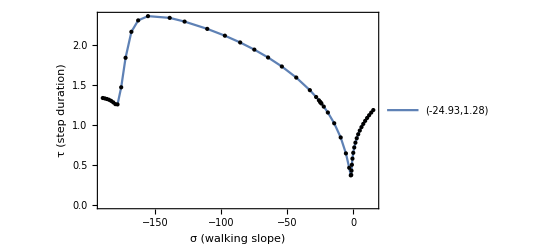

```mathematica
PlotGaitParameters[Mv, "i" -> {"σ", "τ"}]
```

## Get Target Actuated Gait

```mathematica
i = σi;
h = <||>;
c = SortGaits[Mv, σmin]⟦1, "c", 1⟧;
h0 = c⟦i⟧-σdes;
f = "v";
m = 1;
d = Negative;
file = None;
seed1 = {{i, h, c, h0, f, m, d, file}};
M1 = Join@@finecurve[seed1];
```

c: {0.231966,-0.458976,4.24226,-4.73344,0.00247792,0.7,0.198126,-0.85523,-0.0828622,0.48693,0.,0.649939}

OptionValue::nodef: Unknown option max for cmnat.

General::stop: Further output of OptionValue::nodef will be suppressed during this calculation.

tmon --- tree depth: 1 |M|: 2 |Q|: 1 t: 46.26 s t/|M|: 23.13 s/pt

## Create Slope Slice

```mathematica
cσ = SortGaits[M1, σmin]⟦1, "c", 1⟧;
h0 = 0.02;
f = "σ";
m = 25;
d = If[# == "p", Positive, Negative]&;
file = "g1_σ_0_" <> #&;
seeds = {{cσ, h0, f, m, d["p"], file["p"]}, {cσ, h0, f, m, d["n"], file["n"]}} ;
Mσ = Join@@coarsecurve[seeds];
```

c: {0.2241,-0.448201,4.15504,-4.64815,0.,0.7,0.190487,-0.860977,-0.0796605,0.472259,0.,0.634941}

c: {0.2241,-0.448201,4.15504,-4.64815,0.,0.7,0.190487,-0.860977,-0.0796605,0.472259,0.,0.634941}

writing to: csv\g1_σ_0_p_Z_F_2_Z.csv

writing to: csv\g1_σ_0_n_Z_F_2_Z.csv

ContinuationMethods`Private`corrector::step: The norm of the step size for {0.201992,-0.403984,3.08099,-3.35487,-4.11938×10^-17,0.431102,0.0786815,-0.387823,-0.0906624,0.294382,«2»} is 9.62963 (> 2); the search is likely to diverge.

ContinuationMethods`Private`corrector::step: The norm of the step size for {0.200196,-0.400391,2.97496,-3.21675,2.52164×10^-18,0.392863,0.0710828,-0.333063,-0.0994235,0.275142,«2»} is 4.4912 (> 2); the search is likely to diverge.

ContinuationMethods`Private`corrector::step: The norm of the step size for {0.200166,-0.400333,2.89439,-3.10834,5.07403×10^-19,0.358959,0.0655003,-0.284566,-0.109445,0.257547,«2»} is 5.65619 (> 2); the search is likely to diverge.

General::stop: Further output of ContinuationMethods`Private`corrector::step will be suppressed during this calculation.

ContinuationMethods`Private`corrector::cvmit: Failed to converge within 10 iterations; starting from {0.205968,-0.411937,2.78488,-2.95925,-7.46609×10^-19,0.304812,0.0589672,-0.205513,-0.129975,0.22431,«2»} the final error was 0.0000994224.

tmon --- tree depth: 25 |M|: 26 |Q|: 1 t: 1372.00 s t/|M|: 52.78 s/pt

ContinuationMethods`Private`corrector::cvmit: Failed to converge within 10 iterations; starting from {0.172236,-0.344472,-1.04873,0.684254,-1.16754×10^-18,0.156025,0.00495513,-0.0359484,-0.0482277,-0.0401757,«2»} the final error was 0.00271339.

tmon --- tree depth: 25 |M|: 26 |Q|: 1 t: 1966.00 s t/|M|: 75.60 s/pt

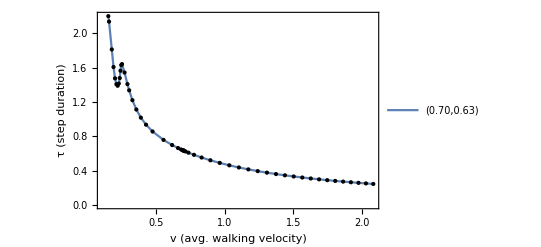

```mathematica
PlotGaitParameters[Mσ, "i" -> {"v", "τ"}]
```

## Create Detailed Slices

```mathematica
round[v_, h0_] := Module[{m, p},
p = Ceiling[v, h0] - v;
m = v - Floor[v, h0];
<|{-1} -> m, {1} -> p|>
];
```

```mathematica
MinMax@Mv⟦All, "c", 1, σi⟧/Degree
MinMax@Mσ⟦All, "c", 1, vi⟧
```

{-189.898,15.3489}

{0.155145,2.08039}

```mathematica
mσ = 10; (* # points between a unit of σ *)
mv = 1000; (* # points between a unit of v *)

i = {σi, σi, vi, vi};

h = round[cv[[σi]], 1.0 Degree/mσ];
h = {h, h, <||>, <||>};

c = {cv, cv, cσ, cσ};
h0 =N@{Degree/mσ, Degree/mσ, 1/mv, 1/mv};
f = {"v", "v", "σ", "σ"};

m = {mσ/Degree, mσ/Degree, mv, mv};
m = Round[{cv⟦σi⟧+220 Degree, 16Degree - cv⟦σi⟧, cσ⟦vi⟧, 3-cσ⟦vi⟧} m];
d = {Negative, Positive, Negative, Positive};
file = {"g1_f_v_0.7_n", "g1_f_v_0.7_p", "g1_f_σ_0_n", "g1_f_σ_0_p"};
seed2 = MapThread[List, {i, h, c,h0, f, m, d, file}];
M2 = finecurve[seed2];

Mvf = Join@@M2⟦1;;2⟧;
Mσf = Join@@M2⟦3;;4⟧;
```

c: {0.0310525,-0.9324,0.817191,-1.89236,-0.435148,0.7,-1.29489×10^-33,5.45503×10^-18,-1.66199×10^-19,-2.63027×10^-18,0.,1.28427}

c: {0.0310525,-0.9324,0.817191,-1.89236,-0.435148,0.7,-1.29489×10^-33,5.45503×10^-18,-1.66199×10^-19,-2.63027×10^-18,0.,1.28427}

c: {0.2241,-0.448201,4.15504,-4.64815,0.,0.7,0.190487,-0.860977,-0.0796605,0.472259,0.,0.634941}

c: {0.2241,-0.448201,4.15504,-4.64815,0.,0.7,0.190487,-0.860977,-0.0796605,0.472259,0.,0.634941}

writing to: csv\g1_f_v_0.7_n_Z_F_2_Z.csv

writing to: csv\g1_f_v_0.7_p_Z_F_2_Z.csv

writing to: csv\g1_f_σ_0_n_Z_F_2_Z.csv

writing to: csv\g1_f_σ_0_p_Z_F_2_Z.csv

OptionValue::nodef: Unknown option max for cmnat.

General::stop: Further output of OptionValue::nodef will be suppressed during this calculation.

OptionValue::nodef: Unknown option max for cmnat.

General::stop: Further output of OptionValue::nodef will be suppressed during this calculation.

OptionValue::nodef: Unknown option max for cmnat.

General::stop: Further output of OptionValue::nodef will be suppressed during this calculation.

OptionValue::nodef: Unknown option max for cmnat.

General::stop: Further output of OptionValue::nodef will be suppressed during this calculation.

tmon --- tree depth: 409 |M|: 410 |Q|: 1 t: 12840.00 s t/|M|: 31.32 s/pt

tmon --- tree depth: 700 |M|: 701 |Q|: 1 t: 18950.00 s t/|M|: 27.03 s/pt

ContinuationMethods`Private`corrector::cvmit: Failed to converge within 30 iterations; starting from {-3.06418,-1.02051,10.3895,-10.7113,-3.57618,0.7,1.38679,-1.25615,-0.35881,1.03438,«2»} the final error was 0.00322574.

tmon --- tree depth: 1801 |M|: 1801 |Q|: 0 t: 36260.00 s t/|M|: 20.14 s/pt

tmon --- tree depth: 2300 |M|: 2301 |Q|: 1 t: 40740.00 s t/|M|: 17.71 s/pt

```mathematica
PlotGaitParameters[M2, "i" -> {"σ", "v", "τ"}]
```

-Graphics3D-

```mathematica
BLSaveTo["Here", "mx/slices.mx", {Mp, Mp1, Mp2, M0, Mv, M1, Mσ, M2, Mvf, Mσf}];
```

```mathematica
40740.00/3600
```

11.3167